```mathematica
PhasePlot[f_,ic_,ti_,opts___]:=Block[{i,n=Length[ic],ff,ivp,sol,t1,t2,tmin,tmax,phaseplot,ps,pvf,vf,vfr,pev,a,ev,evs,optss},
ff=f /. {x->x[t],y->y[t]};
If[Head[ti]===List,{tmin,tmax}=ti,{tmin,tmax}={-ti,ti}];
pfv=VectorField /. {opts,VectorField->False};
pev=EigenVectors /. {opts,EigenVectors->False};
ps=PlotStyle /.{opts,PlotStyle->{}};
optss=DeleteCases[{opts},VectorField->_];
optss=DeleteCases[optss,EigenVectors->_];
optss=DeleteCases[optss,PlotStyle->_];
optss[[0]]=Sequence;
vf=Graphics[];
ev=Graphics[];
vfr=PlotRange /. {opts, PlotRange->{{-1,1},{-1,1}}};
If[pfv,vf=VectorPlot[f,{x,vfr[[1,1]],vfr[[1,2]]},{y,vfr[[2,1]],vfr[[2,2]]},Frame->False,Axes->True,Ticks->False,VectorPoints->8,VectorScale->{0.1,0.3}]];
If[pev,
a=Transpose[{f/. {x->1,y->0},f/. {x->0,y->1}}];
evs=Eigensystem[a][[2]];
If[Im[evs]=={{0,0},{0,0}},
ev=ParametricPlot[evs t,{t,-100,100},PlotStyle->{Red,Red}]];
];
Off[NDSolve::"ndsz"];
Do[
ivp={x'[t]==ff[[1]],y'[t]==ff[[2]],x[0]==ic[[i,1]],y[0]==ic[[i,2]]};
sol=NDSolve[ivp,{x[t],y[t]},{t,tmin,tmax}];
{t1,t2}=sol[[1]][[1]][[2]][[0]][[1]][[1]];
phaseplot[i]=ParametricPlot[{x[t],y[t]} /. sol,{t,t1,t2},PlotStyle->ps]
,{i,1,n}];
On[NDSolve::"ndsz"];
Show[Table[phaseplot[i],{i,1,n}],vf,ev,optss]
];
```

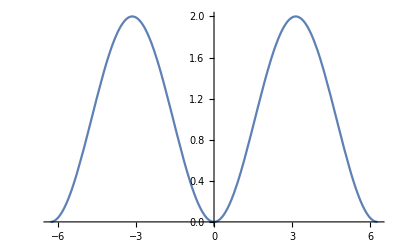

```mathematica
U[x_]=1−Cos[x];
Plot[U[x],{x,−2Pi,2Pi},Ticks->None]
```

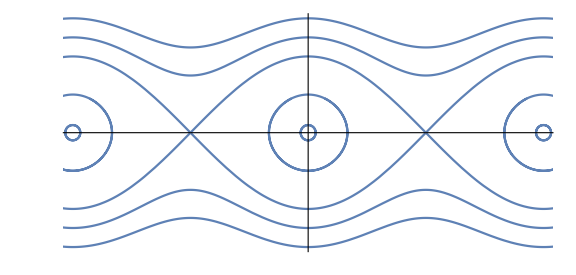

```mathematica
undampedPend = PhasePlot[{y,-Sin[x]},{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3}},2π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

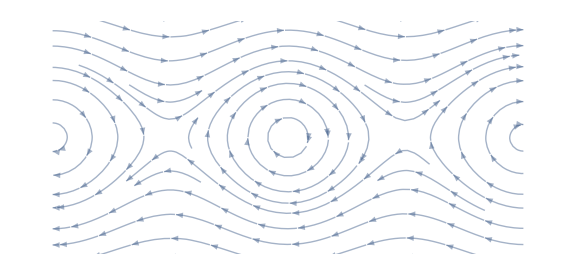

```mathematica
undampedPendVec=StreamPlot[{y, -Sin[x]},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

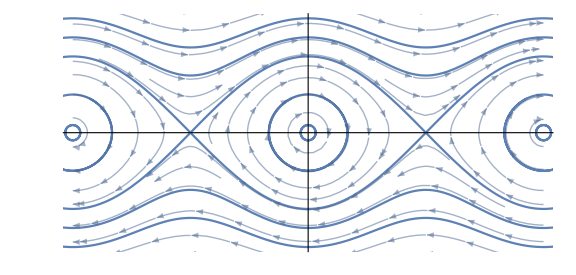

```mathematica
undampedPendComb = Show[undampedPend,undampedPendVec]
```

```mathematica
Export["undampedPendComb.pdf",undampedPendComb]
```

undampedPendComb.pdf

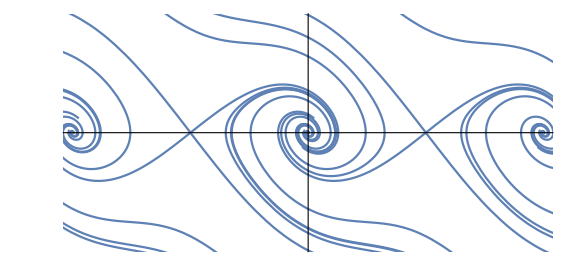

```mathematica
damped05=PhasePlot[{y,-0.5y-Sin[x]},
{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},
{Pi,-0.01},{Pi,0.01},{-Pi,-0.01},{-Pi,0.01}},4π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

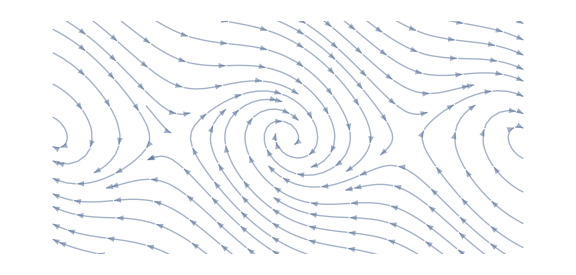

```mathematica
damped05Vec=StreamPlot[{y, -0.5y-Sin[x]},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

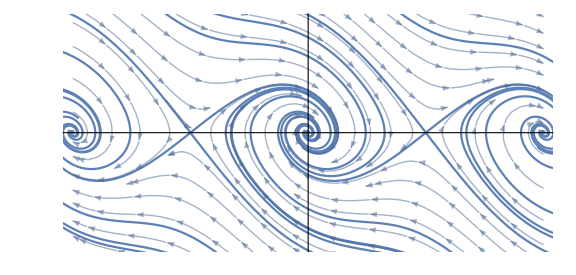

```mathematica
damped05Comb = Show[damped05,damped05Vec]
```

```mathematica
Export["damped05Comb.pdf",damped05Comb]
```

damped05Comb.pdf

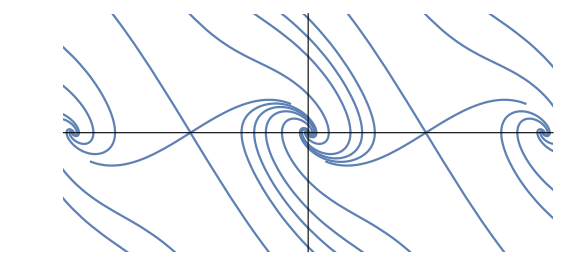

```mathematica
damped1 = PhasePlot[{y,-1y-Sin[x]},
{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3},
{Pi,-0.01},{Pi,0.01},{-Pi,-0.01},{-Pi,0.01}},3.5π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

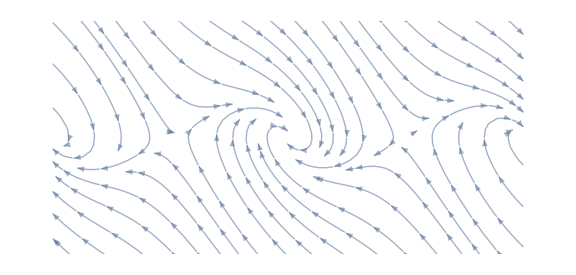

```mathematica
damped1Vec=StreamPlot[{y, -1y-Sin[x]},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

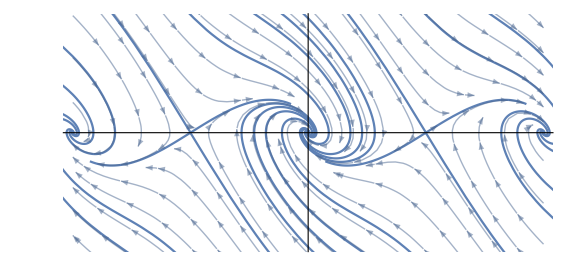

```mathematica
damped1Comb = Show[damped1,damped1Vec]
```

```mathematica
Export["damped1Comb.pdf",damped1Comb]
```

damped1Comb.pdf

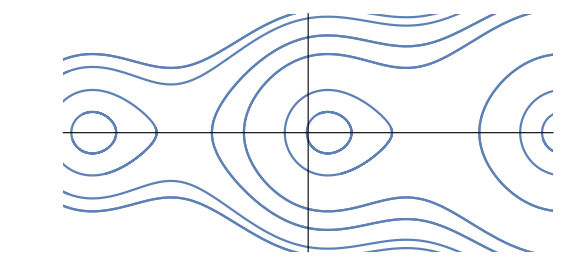

```mathematica
torque05 = PhasePlot[{y,-Sin[x]+0.5},{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3}},2π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

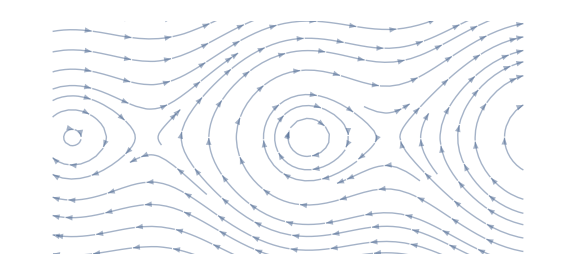

```mathematica
torque05Vec=StreamPlot[{y, -Sin[x]+0.5},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

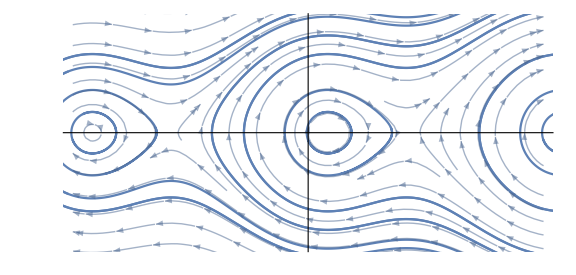

```mathematica
torque05Comb = Show[torque05,torque05Vec]
```

```mathematica
Export["torque05Comb.pdf",torque05Comb]
```

torque05Comb.pdf

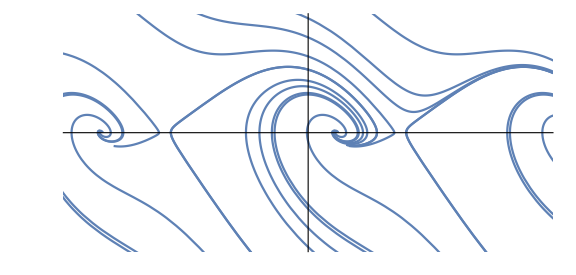

```mathematica
torque07damped07=PhasePlot[{y,-0.7y-Sin[x]+0.7},
{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3},
{5Pi/6,-0.01},{5Pi/6,0.01},{-7Pi/6,-0.01},{-7Pi/6,0.01}},3.5π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

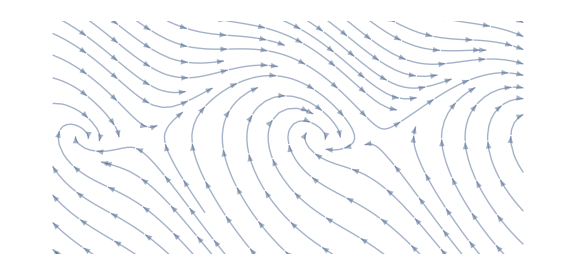

```mathematica
torque07damped07Vec=StreamPlot[{y, -0.7y-Sin[x]+0.7},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

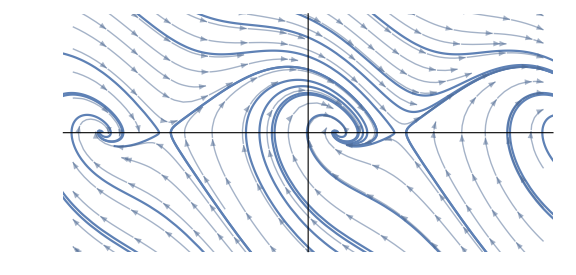

```mathematica
torque07damped07Comb = Show[torque07damped07,torque07damped07Vec]
```

```mathematica
Export["torque07damped07Comb.pdf",torque07damped07Comb]
```

torque07damped07Comb.pdf

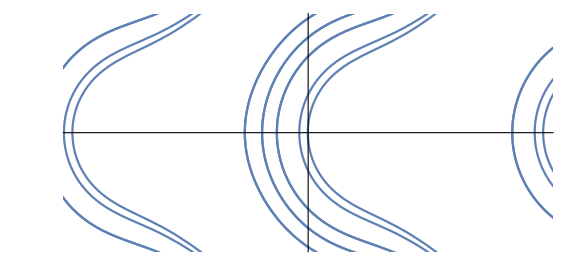

```mathematica
torque2=PhasePlot[{y,-Sin[x]+2},{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3}},2π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

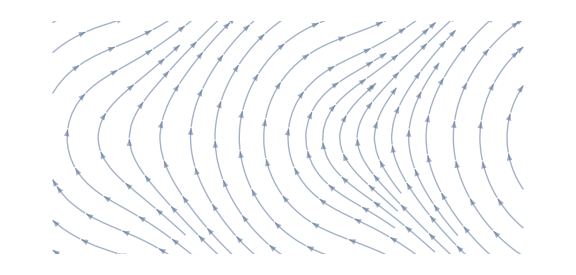

```mathematica
torque2Vec=StreamPlot[{y, -Sin[x]+2},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

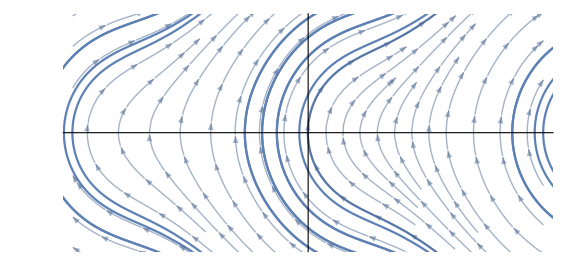

```mathematica
torque2Comb = Show[torque2,torque2Vec]
```

```mathematica
Export["torque2Comb.pdf",torque2Comb]
```

torque2Comb.pdf

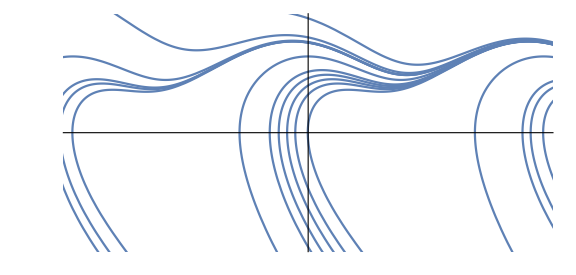

```mathematica
torque2damped1=PhasePlot[{y,-1y-Sin[x]+2},{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3}},2π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

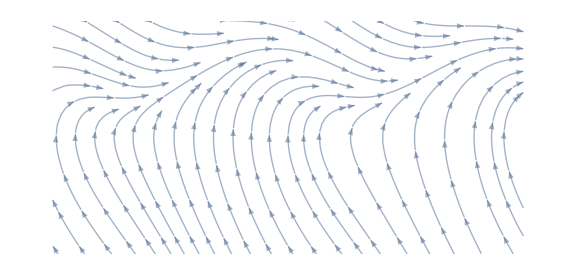

```mathematica
torque2damped1Vec=StreamPlot[{y, -1y-Sin[x]+2},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

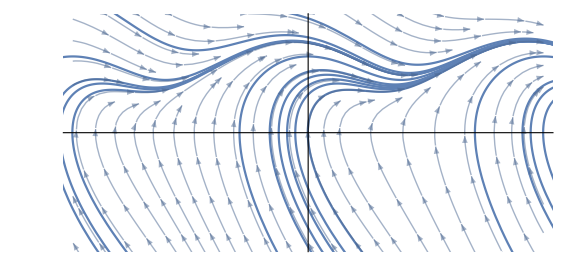

```mathematica
torque2damped1Comb = Show[torque2damped1,torque2damped1Vec]
```

```mathematica
Export["torque2damped1Comb.pdf",torque2damped1Comb]
```

torque2damped1Comb.pdf

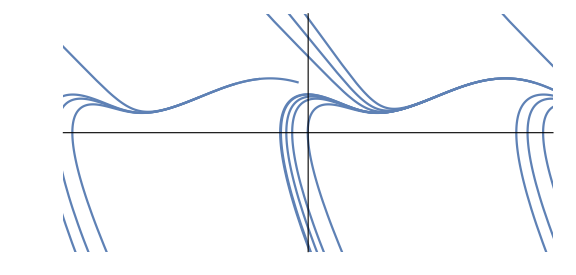

```mathematica
torque2damped2=PhasePlot[{y,-2y-Sin[x]+2},{{0,0.2},{0,1},{-2π,0.2},{-2π,1},{2π,0.2},{2π,1},{0,2},{2π,-2},{2π,2},{-2π,-2},{-2π,2},{0,-2},{0,2.5},{0,-2.5},{0,3},{0,-3}},2π,PlotRange->{{-2π,2π},{-3,3}},Ticks->False,ImageSize->Large]
```

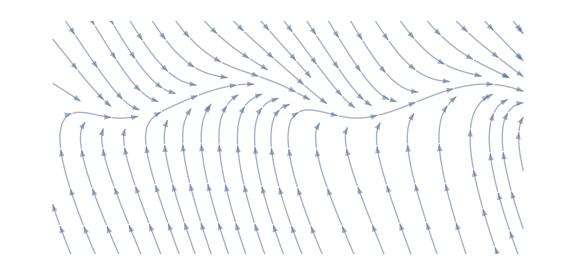

```mathematica
torque2damped2Vec=StreamPlot[{y, -2y-Sin[x]+2},{x,-2Pi,2Pi},{y,-2Pi,2Pi},PlotRange->{{-2π,2π},{-3,3}},ImageSize->Large,AspectRatio->Automatic,Frame->False,StreamStyle->Opacity[0.5]]
```

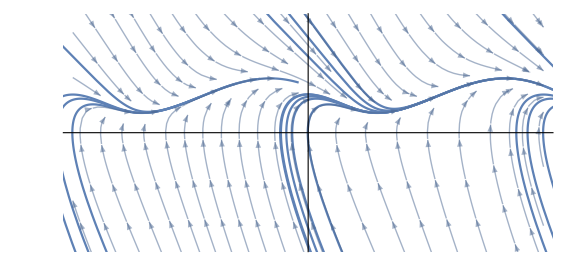

```mathematica
torque2damped2Comb = Show[torque2damped2,torque2damped2Vec]
```

```mathematica
Export["torque2damped2Comb.pdf",torque2damped2Comb]
```

torque2damped2Comb.pdf